```mathematica
Import["ToMatlab.m"]
```

Import::nffil: File ToMatlab.m not found during Import.

```mathematica
f[t_]=Exp[-(t)^2/Sqrt[0.2]]
```

ⅇ^(-2.23607 t^2)

```mathematica
K[k_,u_,aa_,bb_,dd_]=Exp[{k^2}*ⅈ*Pi*(aa/bb)]*Exp[-u*k*ⅈ*2*Pi*(1/bb)]*Exp[{u^2}*ⅈ*Pi*(dd/bb)]
```

{ⅇ^((ⅈ aa k^2 π)/bb-(2 ⅈ k π u)/bb+(ⅈ dd π u^2)/bb)}

```mathematica
a1=3
b1=5
d1=5
```

3

5

5

```mathematica
LCT1[u_]=Simplify[Integrate[f[t]*K[t,u,a1,b1,d1], {t,-Infinity,Infinity}]]
```

{(0.973533+0.35559 ⅈ) ⅇ^((-0.10321+3.05459 ⅈ) u^2)}

```mathematica
ToMatlab[LCT1[u]]
```

ToMatlab[{(0.973533+0.35559 ⅈ) ⅇ^((-0.10321+3.05459 ⅈ) u^2)}]

```mathematica
a2=-1
b2=1/2
d2=4
```

-1

1/2

4

```mathematica
LCT2[u_]=Simplify[Integrate[f[t]*K[t,u,a2,b2,d2], {t,-Infinity,Infinity}]]
```

{(0.560801-0.395677 ⅈ) ⅇ^((-1.9847+30.7096 ⅈ) u^2)}

```mathematica
ToMatlab[LCT2[u]]
```

ToMatlab[{(0.560801-0.395677 ⅈ) ⅇ^((-1.9847+30.7096 ⅈ) u^2)}]

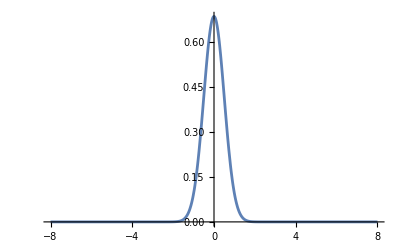

```mathematica
Plot[Evaluate[Abs[LCT2[u]]],{u,-8,8}, PlotRange-> All]
```

```mathematica
fshift[t_,k_]=LCT1[t-(k/2)]
Newfo[t_]=Simplify[Conjugate[LCT2[t]], t∈Reals]
fconjshift[t_,k_]=Newfo[t+(k/2)]
ROFf[t_,k_]= Simplify[fshift[t,k]*fconjshift[t,k]]
```

{(0.973533+0.35559 ⅈ) ⅇ^((-0.10321+3.05459 ⅈ) (-k/2+t)^2)}

{(0.560801+0.395677 ⅈ) ⅇ^((-1.9847-30.7096 ⅈ) t^2)}

{(0.560801+0.395677 ⅈ) ⅇ^((-1.9847-30.7096 ⅈ) (k/2+t)^2)}

{(0.40526+0.58462 ⅈ) ⅇ^((-0.521978-6.91375 ⅈ) k^2-(1.88149+33.7642 ⅈ) k t-(2.08791+27.655 ⅈ) t^2)}

```mathematica
ToMatlab[ROFf[u,k]]
```

ToMatlab[{(0.40526+0.58462 ⅈ) ⅇ^((-0.521978-6.91375 ⅈ) k^2-(1.88149+33.7642 ⅈ) k u-(2.08791+27.655 ⅈ) u^2)}]

```mathematica
a=1
b=2
d=0
```

1

2

0

```mathematica
BDF[t_,u_]=Simplify[Integrate[ROFf[t,k]*K[k,u,a,b,d],{k,-Infinity,Infinity}]]
```

{1/(1. t+(0.0927571+0.00516884 ⅈ) u)(0.40526+0.58462 ⅈ) ⅇ^((-2.08791-27.655 ⅈ) t^2) (1. ⅇ^((0.00452797-0.0463482 ⅈ) ((-1.88149-33.7642 ⅈ) t-(0.+3.14159 ⅈ) u)^2.) ((-1.88149-33.7642 ⅈ) t-(0.+3.14159 ⅈ) u)^1. ((0.00712128+0.00878757 ⅈ)-(0.00878757-0.00712128 ⅈ) Erfi[(0.144984+0.159839 ⅈ) ((-1.88149-33.7642 ⅈ) t-(0.+3.14159 ⅈ) u)^1.])+1. ⅇ^((0.00452797-0.0463482 ⅈ) ((1.88149+33.7642 ⅈ) t+(0.+3.14159 ⅈ) u)^2.) ((1.88149+33.7642 ⅈ) t+(0.+3.14159 ⅈ) u)^1. ((-0.00712128-0.00878757 ⅈ)+(0.00878757-0.00712128 ⅈ) Erfi[(0.144984+0.159839 ⅈ) ((1.88149+33.7642 ⅈ) t+(0.+3.14159 ⅈ) u)^1.]))}

```mathematica
ToMatlab[BDF[t,u]]
```

ToMatlab[{1/(1. t+(0.0927571+0.00516884 ⅈ) u)(0.40526+0.58462 ⅈ) ⅇ^((-2.08791-27.655 ⅈ) t^2) (1. ⅇ^((0.00452797-0.0463482 ⅈ) ((-1.88149-33.7642 ⅈ) t-(0.+3.14159 ⅈ) u)^2.) ((-1.88149-33.7642 ⅈ) t-(0.+3.14159 ⅈ) u)^1. ((0.00712128+0.00878757 ⅈ)-(0.00878757-0.00712128 ⅈ) Erfi[(0.144984+0.159839 ⅈ) ((-1.88149-33.7642 ⅈ) t-(0.+3.14159 ⅈ) u)^1.])+1. ⅇ^((0.00452797-0.0463482 ⅈ) ((1.88149+33.7642 ⅈ) t+(0.+3.14159 ⅈ) u)^2.) ((1.88149+33.7642 ⅈ) t+(0.+3.14159 ⅈ) u)^1. ((-0.00712128-0.00878757 ⅈ)+(0.00878757-0.00712128 ⅈ) Erfi[(0.144984+0.159839 ⅈ) ((1.88149+33.7642 ⅈ) t+(0.+3.14159 ⅈ) u)^1.]))}]